```mathematica
nohole=Import["/Users/cal/Documents/DSMC_Simulations/12_13_20_CaOH/flow_4.00000_T_2.00000_nohole/data/particles_omega_0.00000_M_57.0_zmax_0.10609_pflip_0.10000_job_11247355.out","Table",HeaderLines->3];
hole=Import["/Users/cal/Documents/DSMC_Simulations/12_13_20_CaOH/flow_4.00000_T_2.00000_hole/data/particles_omega_0.00000_M_57.0_zmax_0.10609_pflip_0.10000_job_11247072.out","Table",HeaderLines->3];
```

```mathematica
vn=√Total[#^2]&/@nohole[[All,{8,9,10}]];
vh=√Total[#^2]&/@hole[[All,{8,9,10}]];
```

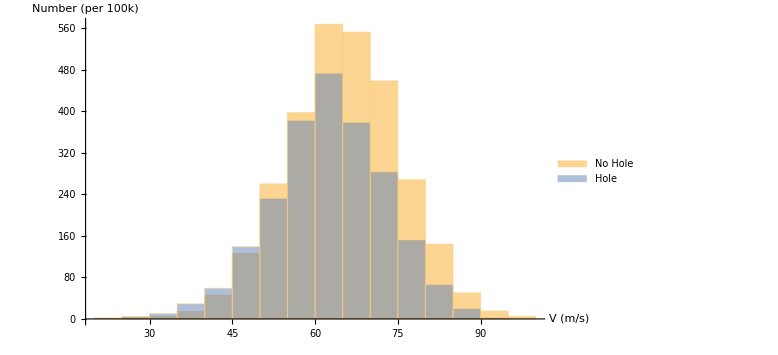

```mathematica
Histogram[{vn,vh},ChartLegends->{"No Hole", "Hole"},AxesLabel->{"V (m/s)","Number (per 100k)"},ImageSize->Large]
```

Extraction without and with hole:

```mathematica
Length@vn/100000.
Length@vh/100000.
```

0.02911

0.02231